```mathematica
Off[General::spell1];
Off[General::spell];
SetDirectory["/Users/heatherchen/PycharmProjects/project/ecma33330_proj/blsdata-retrieve/output"]
```

/Users/heatherchen/PycharmProjects/project/ecma33330_proj/blsdata-retrieve/output

#### Define the HP Filter

```mathematica
Trend[vec_,smooth_]:=Module[{T,A,B},T=Length[vec];
A=Append[Append[Prepend[Prepend[Table[PadRight[PadLeft[{-1,4,-6,4,-1},t+2],T],{t,3,T-2}],PadRight[{2,-5,4,-1},T]],PadRight[{-1,2,-1},T]],PadLeft[{-1,4,-5,2},T]],PadLeft[{-1,2,-1},T]];
B=Inverse[IdentityMatrix[T]-N[smooth] A];
Exp[B.Log[N[vec]]]];

Detrend[vec_,smooth_]:=Log[vec]-Log[Trend[vec,smooth]];
```

#### Set the HP Filter parameter to my preferred high value.

```mathematica
smooth = 10^5;
```

#### Set the start year.

```mathematica
start=1976;
```

#### Import monthly data on Unemployment, Employment, Short-term Employment, and Help-Wanted Advertisements. Adjust the Short-Term Unemployment Rate Data to Account for the CPS Redesign.

The first 517 elements of the short-term unemployment rate series are fine.  On and after February 1994, the data are messed up by the January 1994 CPS Redesign.   See Appendix A in  "Reassessing the Ins and Outs of Unemployment," January 28, 2005 version.  I correct this using the CPS microdata.

```mathematica
UnempM=Import["unemp.txt","Lines"];
Print[UnempM⟦1⟧];
UnempM=ToExpression@@{Drop[UnempM,1]};

EmpM=Import["emp.txt","Lines"];
Print[EmpM⟦1⟧];
EmpM=ToExpression@@{Drop[EmpM,1]};

ShortM=Import["short.txt","Lines"];
Print[ShortM⟦1⟧];
ShortM=ToExpression@@{Drop[ShortM,1]};

ShortShareM=Import["shortadj.txt","Lines"];
Print[ShortShareM⟦1⟧];ShortShareM=ToExpression@@{Drop[ShortShareM,1]};
ShortAdjM=ShortShareM*Take[UnempM,{12(1976-start)+1,12(1976-start)+Length[ShortShareM]}];
ShortAdjM=Flatten[Prepend[ShortAdjM,Take[ShortM,12(1976-start)]]];
```

Unemployment

Employment

2749

test.d11

#### Figure out the longest available data series and print the stopping date.

```mathematica
available =Min[{Length[UnempM],Length[EmpM],Length[ShortAdjM]}];
UnempM=Take[UnempM,available];EmpM=Take[EmpM,available];HelpM=Take[HelpM,available];ShortAdjM=Take[ShortAdjM,available];
Print[IntegerPart[start+available/12],":M",available-12IntegerPart[available/12]];
dateM[x_]:=Transpose[{Table[start+(i-1)/12.,{i,1,Length[x]}],x}];dateQ[x_]:=Transpose[{Table[start+(i-1)/4.,{i,1,Length[x]}],x}];
```

2005:M1

#### Construct the unemployment rate, led by one period.

```mathematica
UrateM=Drop[UnempM/(UnempM+EmpM),1];
```

#### Plot the Adjustment to the Short Term Unemployment Rate time series.

```mathematica
ListPlot[{dateM[ShortAdjM],dateM[ShortM]},Joined->True,PlotStyle->{Hue[0],Hue[2/3]},PlotLegends->{"Adjusted","Published Data"},PlotLabel->"Short Term Unemployment",Filling->None];
```

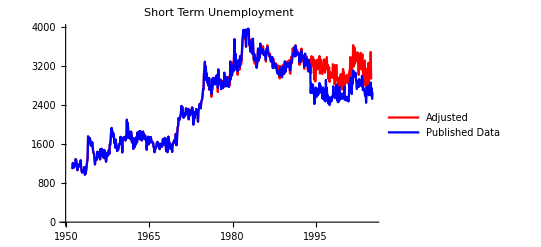

```mathematica
%163
```

#### Construct the Job Finding Probability F according to "Reassessing the Ins and Outs of Unemployment," January 28, 2005 version, Equation (4).

```mathematica
FindM=1.-(Drop[UnempM,1]-Drop[ShortAdjM,1])/Drop[UnempM,-1];
findM=-Log[1-FindM];
```

#### Construct the Separation Rate s according to Equation 5.

```mathematica
t=1;sepM={};While[t<Length[UnempM],sepM=Append[sepM,s/.FindRoot[UnempM⟦t+1⟧==((1-ⅇ^(-findM⟦t⟧-s)) s (UnempM⟦t⟧+EmpM⟦t⟧))/(findM⟦t⟧+s)+ⅇ^(-findM⟦t⟧-s) UnempM⟦t⟧,{s,0.03}]];t+=1];

SepM=1-ⅇ^-sepM;
```

#### Compute Quarterly Averages

```mathematica
findQ=1/3 Plus@@Transpose[Partition[findM,3]];
UrateQ=1/3 Plus@@Transpose[Partition[UrateM,3]];
sepQ=1/3 Plus@@Transpose[Partition[sepM,3]];
HelpQ=Plus@@Transpose[Partition[HelpM,3]];
UnempQ=Plus@@Transpose[Partition[UnempM,3]];
```

#### Export Data for LaTeX

```mathematica
Export["find.dat",dateQ[findQ]];
Export["urate.dat",dateQ[N[UrateQ]]];
Export["sep.dat",dateQ[sepQ]];
Export["theta.dat",dateQ[N[(100HelpQ)/UnempQ]]];
Export["uss.dat",dateQ[N[sepQ/(sepQ+findQ)]]];
Export["uf.dat",dateQ[N[Mean[sepQ]/(Mean[sepQ]+findQ)]]];
Export["us.dat",dateQ[N[sepQ/(sepQ+Mean[findQ])]]];
```

#### Print the Correlation between the job finding and unemployment rates and between the separation and unemployment rates.

```mathematica
Print[Correlation[Detrend[findQ,smooth],Detrend[UrateQ,smooth]]];
Print[Correlation[Detrend[sepQ,smooth],Detrend[UrateQ,smooth]]];
Print[Correlation[Detrend[findQ,smooth],Detrend[HelpQ/UnempQ,smooth]]];
```

-0.965227

0.649282

0.961209

#### Print the output of a regression of "Hypothetical" unemployment rates (only changes in f or only changes in s) on the actual unemployment rate.

```mathematica
Print[LinearModelFit[Transpose[{Detrend[UrateQ,smooth],Detrend[Mean[sepQ]/(Mean[sepQ]+findQ),smooth]}],{1,x},x]];
Print[LinearModelFit[Transpose[{Detrend[UrateQ,smooth],Detrend[sepQ/(sepQ+Mean[findQ]),smooth]}],{1,x},x]];
```

FittedModel[1.90959×10^-10+0.791154 x]

FittedModel[6.40277×10^-10+0.216992 x]

#### Do the same, dropping the earlier time period.

```mathematica
z=140;Print[start+z/4-1];
Print[LinearModelFit[Drop[Transpose[{Detrend[UrateQ,smooth],Detrend[Mean[sepQ]/(Mean[sepQ]+findQ),smooth]}],z],{1,x},x]];
Print[LinearModelFit[Drop[Transpose[{Detrend[UrateQ,smooth],Detrend[sepQ/(sepQ+Mean[findQ]),smooth]}],z],{1,x},x]];
```

1985

FittedModel[0.00773053+0.949431 x]

FittedModel[-0.00764935+0.0501814 x]

#### Construct the hypothetical unemployment rate with changes only in vacancies

```mathematica
t=1;hyp=h/.Solve[(1-h)Mean[SepM]==0.017 h^0.5 HelpM[[t]]^0.5,h];
While[t<Length[HelpM],t+=1;hyp=Append[hyp,Last[hyp]+(1-Last[hyp])Mean[SepM]-0.017 Last[hyp]^0.5 HelpM[[t]]^0.5]];
hypQ=1/3 Plus@@Transpose[Partition[hyp,3]];
Export["hyp.dat",dateQ[hypQ]];
Export["hypt.dat",dateQ[Trend[hypQ,smooth]]];
Export["hypd.dat",dateQ[Detrend[hypQ,smooth]]];
Export["uratet.dat",dateQ[Trend[N[UrateQ],smooth]]];
Export["urated.dat",dateQ[Detrend[N[UrateQ],smooth]]];
```